```mathematica
symboliclegendre[n_,x_]:=Solve[LegendreP[n,x]==0];
legendreprime[n_,a_]:=D[LegendreP[n,x],x]/. x->a;
weights[n_,x_]:=2/((1-x^2) legendreprime[n,x]^2);

(*how many terms should be generated*)
h=64;

(*what numerical precision is desired?*)
precision=256;

str=OpenWrite["lgvalues.txt"];
Write[str,"abcissae"];
Do[Write[str];Write[str,n];Write[str];
nlist=symboliclegendre[n,x];
xnlist=x/. nlist;
Do[Write[str,N[Part[xnlist,i],precision]],{i,Length[xnlist]}];,{n,2,h}];
Write[str,"weights"];
Do[Write[str];Write[str,n];Write[str];
slist:=symboliclegendre[n,x];
xslist=x/. slist;
Do[Write[str,N[weights[n,Part[xslist,i]],precision]],{i,Length[xslist]}];,{n,2,h}];
Close[str];
```

Finite element example
https://reference.wolfram.com/language/FEMDocumentation/guide/FiniteElementMethodGuide.html

```mathematica
NDEigensystem[-Laplacian[u[x], {x}], u[x], {x, 0, π}, 4]
```

{{3.84029×10^-14,1.,4.00005,9.00061},{InterpolatingFunction[…][x],InterpolatingFunction[…][x],InterpolatingFunction[…][x],InterpolatingFunction[…][x]}}

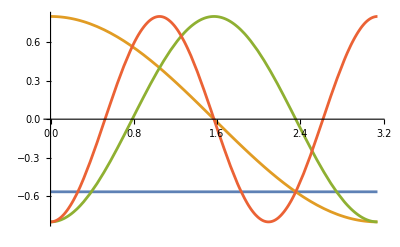

```mathematica
NDEigensystem[-Laplacian[u[x],{x}],u[x],{x,0,π},4];
Plot[Evaluate[%[[2]]],{x,0,π}]
```

```mathematica
{vals,funs}=NDEigensystem[{x+Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈Disk[],6];
```

```mathematica
MatrixForm[%30]
```

(5.78323 | 14.6827 | 14.6827 | 26.3784 | 26.3791 | 30.4787
InterpolatingFunction[…][x,y] | InterpolatingFunction[…][x,y] | InterpolatingFunction[…][x,y] | InterpolatingFunction[…][x,y] | InterpolatingFunction[…][x,y] | InterpolatingFunction[…][x,y])

```mathematica
Flatten[%31]
```

{5.78323,14.6827,14.6827,26.3784,26.3791,30.4787,InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y]}

```mathematica
Length[%33]
```

12

```mathematica
vals
```

{5.78323,14.6827,14.6827,26.3784,26.3791,30.4787}

```mathematica
Table[Plot3D[funs[[i]],{x,y}∈Disk[],PlotRange->All,PlotLabel->vals[[i]],PlotTheme->"Minimal"],{i,Length[vals]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
Ω=ImplicitRegion[1<=x^2+y^2<=2^2&&x-y>=0&&x>=0&&y>=0,{x,y}];
Show[RegionPlot[Ω],ContourPlot[y-x==0,{x,1/Sqrt[2],2},{y,-0.1,Sqrt[2]},ContourStyle->Blue],ContourPlot[y==0,{x,1,2},{y,-0.1,Sqrt[2]},ContourStyle->Green],AspectRatio->Automatic]
```

-Graphics-

```mathematica
pde1=-Laplacian[u[x,y],{x,y}]==If[1.4<=x<=1.6&&0<=y<=0.1,1,0];
pde2=-D[u[x,y]+5*Sin[x]*Sin[y],x,y]==If[1.4<=x<=1.6&&0<=y<=0.1,1,0];
pde= -Laplacian[u[x,y],{x,y}]-D[u[x,y]+5*Sin[x]*Sin[y],x,y]==If[1.4<=x<=1.6&&0<=y<=0.1,1,0];
mapping=Last[FindGeometricTransform[{{1,0},{2,0}},{{1/Sqrt[2],1/Sqrt[2]},{Sqrt[2],Sqrt[2]}}]];
Subscript[Γ,P]=PeriodicBoundaryCondition[u[x,y],y-x==0,mapping];
Subscript[Γ,D]=DirichletCondition[u[x,y]==0,(x^2+y^2==1||x^2+y^2==4)&&!(y-x)>-10^-7];
```

```mathematica
ufun=NDSolveValue[{pde,Subscript[Γ,P],Subscript[Γ,D]},u,{x,y}∈Ω];
```

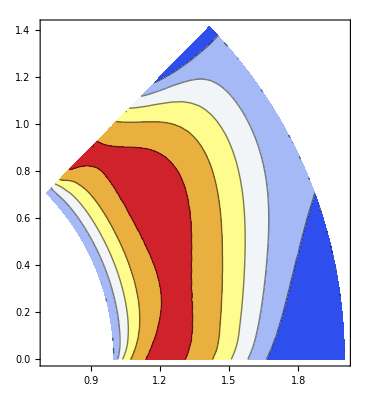

```mathematica
ContourPlot[ufun[x,y],{x,y}∈Ω,ColorFunction->"TemperatureMap",AspectRatio->Automatic]
```